```mathematica
btst[a_]:=Block[{btp},
f[x_]:=a*x;
btp=f[2]+f[2];
btp
];
```

```mathematica
btst[2.]
```

8.

```mathematica
ArrayFlatten[{{H11,H1M[tM1ϕ1],0,0,0,0,0},{HM1[tM1ϕ1],HMM,HM2[tM1ϕ2],0,0,0,0},{0,H2M[tM1ϕ2],H22,H1M[tM2ϕ1],0,0,0},{0,0,HM1[tM2ϕ1],HMM,HM2[tM2ϕ2],0,0},{0,0,0,H2M[tM2ϕ2],H11,H1M[tM3ϕ1],0},{0,0,0,0,HM1[tM3ϕ1],HMM,HM2[tM3ϕ2]},{0,0,0,0,0,H2M[tM3ϕ2],H22}}]
```

SparseArray[<29300>, {4200, 4200}]

```mathematica
H0=H[0.];
Transpose[Sort[Transpose[Eigensystem[H0,-10]]]]
```

Transpose[Transpose[Eigensystem[Hsp,-10]]]

```mathematica
H0[[1,3Nx+1]]
```

0.4

```mathematica
Δl=Join[Table[H0[[i,i+3Nx]],{i,1,Nx}],Table[H0[[i,i+3NxM]],{i,4Nx+1,4Nx+NxM}],Table[H0[[i,i+3Nx]],{i,4Nx+4NxM+1,4Nx+4NxM+Nx}],Table[H0[[i,i+3NxM]],{i,8Nx+4NxM+1,8Nx+4NxM+NxM}],Table[H0[[i,i+3Nx]],{i,8Nx+8NxM+1,8Nx+8NxM+Nx}],Table[H0[[i,i+3NxM]],{i,12Nx+8NxM+1,12Nx+8NxM+NxM}],Table[H0[[i,i+3Nx]],{i,12Nx+12NxM+1,12Nx+12NxM+Nx}]];
```

```mathematica
αl=Join[Table[H0[[i,i+Nx+1]],{i,1,Nx-1}],{H0[[Nx,4Nx+NxM+1]]},Table[H0[[i,i+Nx+1]],{i,4Nx+1,4Nx+NxM-1}],{H0[[4Nx+NxM,4Nx+4NxM+Nx+1]]},Table[H0[[i,i+Nx+1]],{i,4Nx+4NxM+1,4Nx+4NxM+Nx-1}],{H0[[4Nx+4NxM+Nx,8Nx+4NxM+NxM+1]]},Table[H0[[i,i+Nx+1]],{i,8Nx+4NxM+1,8Nx+4NxM+NxM-1}],{H0[[8Nx+4NxM+NxM,8Nx+8NxM+Nx+1]]},Table[H0[[i,i+Nx+1]],{i,8Nx+8NxM+1,8Nx+8NxM+Nx-1}],{H0[[8Nx+8NxM+Nx,12Nx+8NxM+NxM+1]]},Table[H0[[i,i+Nx+1]],{i,12Nx+8NxM+1,12Nx+8NxM+NxM-1}],{H0[[12Nx+8NxM+NxM,12Nx+12NxM+Nx+1]]},Table[H0[[i,i+Nx+1]],{i,12Nx+12NxM+1,12Nx+12NxM+Nx-1}]];
```

```mathematica
Bxl=Join[Table[H0[[i,i+Nx]],{i,1,Nx}],Table[H0[[i,i+NxM]],{i,4Nx+1,4Nx+NxM}],Table[H0[[i,i+Nx]],{i,4Nx+4NxM+1,4Nx+4NxM+Nx}],Table[H0[[i,i+NxM]],{i,8Nx+4NxM+1,8Nx+4NxM+NxM}],Table[H0[[i,i+Nx]],{i,8Nx+8NxM+1,8Nx+8NxM+Nx}],Table[H0[[i,i+NxM]],{i,12Nx+8NxM+1,12Nx+8NxM+NxM}],Table[H0[[i,i+Nx]],{i,12Nx+12NxM+1,12Nx+12NxM+Nx}]];
```

```mathematica
tl=Join[Table[H0[[i,i+1]],{i,1,Nx-1}],{H0[[Nx,4Nx+1]]},Table[H0[[i,i+1]],{i,4Nx+1,4Nx+NxM-1}],{H0[[4Nx+NxM,4Nx+4NxM+1]]},Table[H0[[i,i+1]],{i,4Nx+4NxM+1,4Nx+4NxM+Nx-1}],{H0[[4Nx+4NxM+Nx,8Nx+4NxM+1]]},Table[H0[[i,i+1]],{i,8Nx+4NxM+1,8Nx+4NxM+NxM-1}],{H0[[8Nx+4NxM+NxM,8Nx+8NxM+1]]},Table[H0[[i,i+1]],{i,8Nx+8NxM+1,8Nx+8NxM+Nx-1}],{H0[[8Nx+8NxM+Nx,12Nx+8NxM+1]]},Table[H0[[i,i+1]],{i,12Nx+8NxM+1,12Nx+8NxM+NxM-1}],{H0[[12Nx+8NxM+NxM,12Nx+12NxM+1]]},Table[H0[[i,i+1]],{i,12Nx+12NxM+1,12Nx+12NxM+Nx-1}]];
```

```mathematica
Byl=Join[Table[H0[[i,i]]+μ-ϵ0,{i,1,Nx}],Table[H0[[i,i]]+μ-ϵ0,{i,4Nx+1,4Nx+NxM}],Table[H0[[i,i]]+μ-ϵ0,{i,4Nx+4NxM+1,4Nx+4NxM+Nx}],Table[H0[[i,i]]+μ-ϵ0,{i,8Nx+4NxM+1,8Nx+4NxM+NxM}],Table[H0[[i,i]]+μ-ϵ0,{i,8Nx+8NxM+1,8Nx+8NxM+Nx}],Table[H0[[i,i]]+μ-ϵ0,{i,12Nx+8NxM+1,12Nx+8NxM+NxM}],Table[H0[[i,i]]+μ-ϵ0,{i,12Nx+12NxM+1,12Nx+12NxM+Nx}]];
```

```mathematica
μl=Join[Table[H0[[i,i]]-MagΔY[[i]],{i,1,Nx}],Table[H0[[i,i]]-MagΔY[[i-3Nx]],{i,4Nx+1,4Nx+NxM}],Table[H0[[i,i]]-MagΔY[[i-3Nx-3NxM]],{i,4Nx+4NxM+1,4Nx+4NxM+Nx}],Table[H0[[i,i]]-MagΔY[[i-7Nx-4NxM]],{i,8Nx+4NxM+1,8Nx+4NxM+NxM}],Table[H0[[i,i]]-MagΔY[[i-8Nx-8NxM]],{i,8Nx+8NxM+1,8Nx+8NxM+Nx}],Table[H0[[i,i]]-MagΔY[[i-11Nx-8NxM]],{i,12Nx+8NxM+1,12Nx+8NxM+NxM}],Table[H0[[i,i]]-MagΔY[[i-11Nx-11NxM]],{i,12Nx+12NxM+1,12Nx+12NxM+Nx}]];
```

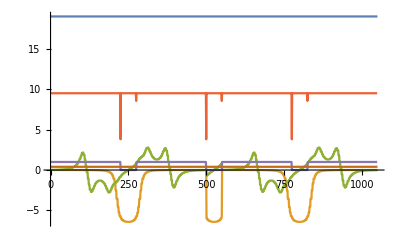

```mathematica
ListPlot[{μl,Byl,Bxl,tl,αl,Δl},PlotRange->All,Joined->True]
```

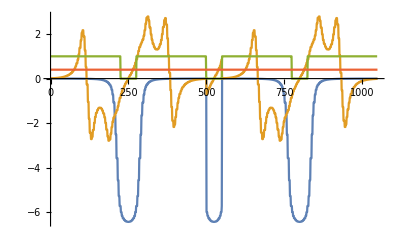

```mathematica
ListPlot[{Byl,Bxl,αl,Δl},PlotRange->All,Joined->True]
```